# Assignment 5

## Part 1

We choose as example problem the Lotka-Volterra equations - the differential equations describing predator-prey relations as follows:

1. A prey population x increases at a rate x’[t] = Ax (proportional to the number of prey) but is simultaneously destroyed by predators at a rate x’[t] = -Bxy (proportional to the product of the numbers of prey and predators).

2. A predator population y decreases at a rate y’[t] = -Cy (proportional to the number of predators), but increases at a rate y’[t] = Dxy (again proportional to the product of the numbers of prey and predators).

This gives the set of coupled equations:

x’[t] = Ax - Bxy
y’[t] = - Cy + Dxy

[http://mathworld.wolfram.com/Lotka-VolterraEquations.html]

```mathematica
Manipulate[Plot[Evaluate[{x[t],y[t]}/.NDSolve[{x'[t]==a x[t]-b x[t] y[t],y'[t]==-c y[t]+d x[t] y[t],x[0]==x0,y[0]==y0},{x[t],y[t]},{t,0,50}]],{t,0,50},PlotRange->All,AxesLabel->{"t","Population"},ImageSize->Large],{a,1,4},{b,1,4},{c,1,4},{d,1,4},{x0,5,20},{y0,5,20}]
```

## Part 2

```mathematica
SerCos[x_,n_]:=Normal[Series[Cos[x1],{x1,0,n}]]/.x1->x
SerSin[x_,n_]:=Normal[Series[Sin[x2],{x2,0,n}]]/.x2->x
```

```mathematica
(* Difference between SerSin and Sin for n=3 *)
```

```mathematica
N[SerSin[2,3]-Sin[2]]
```

-0.242631

```mathematica
N[SerSin[1,3]-Sin[1]]
```

-0.00813765

```mathematica
N[SerSin[0.5,3]-Sin[0.5]]
```

-0.000258872

```mathematica
N[SerSin[0.01,3]-Sin[0.01]]
```

-8.33332×10^-13

```mathematica
(* Difference between SerSin and Sin for n=5 *)
```

```mathematica
N[SerSin[2,5]-Sin[2]]
```

0.0240359

```mathematica
N[SerSin[1,5]-Sin[1]]
```

0.000195682

```mathematica
N[SerSin[0.5,5]-Sin[0.5]]
```

1.54473×10^-6

```mathematica
N[SerSin[0.01,5]-Sin[0.01]]
```

1.73472×10^-18

We now plot the SerSin[x,3] - Sin[x] against x.

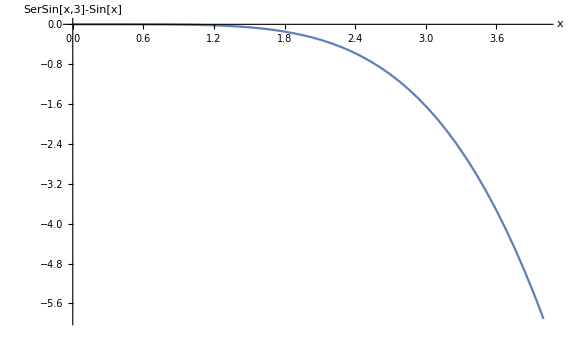

```mathematica
Plot[SerSin[x,3]-Sin[x],{x,0,4},PlotRange->All,ImageSize->Large,AxesLabel->{"x","SerSin[x,3]-Sin[x]"}]
```

We now investigate the behavior of (SerSin[x,n]^2+SerCos[x,n]^2). First, consider algebraically:

```mathematica
SerSinSq[x_,n_]:=Normal[Series[Sin[x1]^2,{x1,0,n}]]/.x1->x
SerCosSq[x_,n_]:=Normal[Series[Cos[x2]^2,{x2,0,n}]]/.x2->x
```

```mathematica
SerSin[x,5]
```

x-x^3/6+x^5/120

```mathematica
(* This is the expansion of SerSin[x,3]^2. *)
```

```mathematica
Normal[Series[SerSin[x,5]^2,{x,0,10}]]
```

x^2-x^4/3+(2 x^6)/45-x^8/360+x^10/14400

```mathematica
(* This is the power series of Sin[x]^2. *)
```

```mathematica
SerSinSq[x,10]
```

x^2-x^4/3+(2 x^6)/45-x^8/315+(2 x^10)/14175

Clearly the series for Sin[x]^2 does not match up with SerSin[x,n]^2. We can observe that this is because squaring the SerSin[x,n] takes care of all terms correctly up to the n^th term - but it also introduces higher order terms that are bound to be inaccurate, since SerSin[x,n] is missing some terms whose product would sum to such higher order terms in SerSinSq[x,n], as we can see in the examples above.

We can see the behavior that the error due to the incorrect higher order terms induces in (SerSin[x,n]^2+SerCos[x,n]^2):

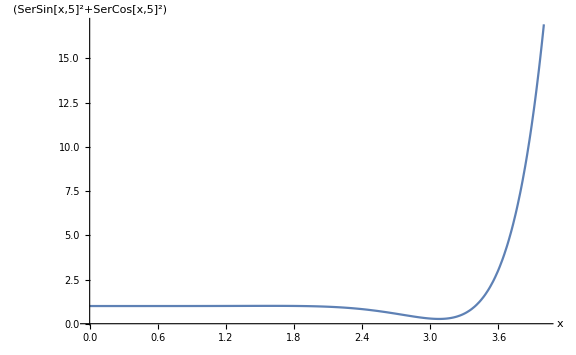

```mathematica
Plot[SerSin[x,5]^2+SerCos[x,5]^2,{x,0,4},PlotRange->All,ImageSize->Large,AxesLabel->{"x","(SerSin[x,5]^2+SerCos[x,5]^2)"}]
```

This confirms our suspicions: as x gets large, the incorrect higher order error terms generate a polynomially increasing error in (SerSin[x,n]^2+SerCos[x,n]^2).

We now observe and compare the behavior of (SerSinSq[x,n]+SerCosSq[x,n]), where SerSinSq[x,n] and SerCosSq[x,n] are the correct power series for Sin^2[x] and Cos^2[x] respectively:

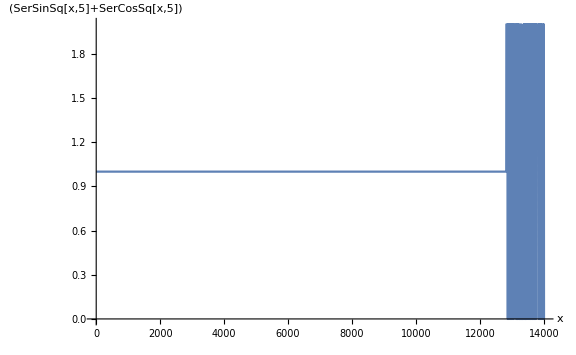

```mathematica
Plot[SerSinSq[x,5]+SerCosSq[x,5],{x,0,14000},PlotRange->All,ImageSize->Large,AxesLabel->{"x","(SerSinSq[x,5]+SerCosSq[x,5])"}]
```

As we can see, this sum remains close to the expected value of 1 for a much longer time than the previous series.

## Part 3

```mathematica
Subscript[R, x][θ_]:={{1,0,0},{0,Cos[θ],-Sin[θ]},{0,Sin[θ],Cos[θ]}}
Subscript[R, y][ζ_]:={{Cos[ζ],0,Sin[ζ]},{0,1,0},{-Sin[ζ],0,Cos[ζ]}}
Subscript[R, z][ϕ_]:={{Cos[ϕ],-Sin[ϕ],0},{Sin[ϕ],Cos[ϕ],0},{0,0,1}}
```

```mathematica
Rot3[ψ_,θ_,ϕ_]:=Subscript[R, z][ψ].Subscript[R, x][θ].Subscript[R, z][ϕ]
```

```mathematica
MatrixForm[Rot3[ψ,θ,ϕ]//Simplify,TableSpacing->{3,3}]
```

(Cos[ϕ] Cos[ψ]-Cos[θ] Sin[ϕ] Sin[ψ] | -Cos[ψ] Sin[ϕ]-Cos[θ] Cos[ϕ] Sin[ψ] | Sin[θ] Sin[ψ]
Cos[θ] Cos[ψ] Sin[ϕ]+Cos[ϕ] Sin[ψ] | Cos[θ] Cos[ϕ] Cos[ψ]-Sin[ϕ] Sin[ψ] | -Cos[ψ] Sin[θ]
Sin[θ] Sin[ϕ] | Cos[ϕ] Sin[θ] | Cos[θ])

```mathematica
Rot3Inverse[ψ_,θ_,ϕ_]:=Subscript[R, z][-ϕ].Subscript[R, x][-θ].Subscript[R, z][-ψ]
```

```mathematica
MatrixForm[Rot3Inverse[ψ,θ,ϕ]//Simplify,TableSpacing->{3,3}]
```

(Cos[ϕ] Cos[ψ]-Cos[θ] Sin[ϕ] Sin[ψ] | Cos[θ] Cos[ψ] Sin[ϕ]+Cos[ϕ] Sin[ψ] | Sin[θ] Sin[ϕ]
-Cos[ψ] Sin[ϕ]-Cos[θ] Cos[ϕ] Sin[ψ] | Cos[θ] Cos[ϕ] Cos[ψ]-Sin[ϕ] Sin[ψ] | Cos[ϕ] Sin[θ]
Sin[θ] Sin[ψ] | -Cos[ψ] Sin[θ] | Cos[θ])

```mathematica
Rot3[ψ,θ,ϕ].Rot3Inverse[ψ,θ,ϕ]//Simplify//MatrixForm
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

The product of Rot3 and Rot3Inverse gives us the identity transformation, as expected. We now try an alternative method for finding an inverse, and show that the inverse obtained is equivalent to the one we have found.

```mathematica
Inverse[Rot3[ψ,θ,ϕ]].Rot3[ψ,θ,ϕ]//Simplify//MatrixForm
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

```mathematica
Inverse[Rot3[ψ,θ,ϕ]]-Rot3Inverse[ψ,θ,ϕ]//Simplify//MatrixForm
```

(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)